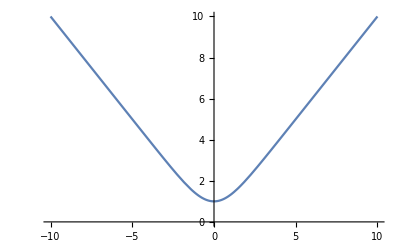

```mathematica
Plot[x*Coth[x],{x,-10,10}]
```

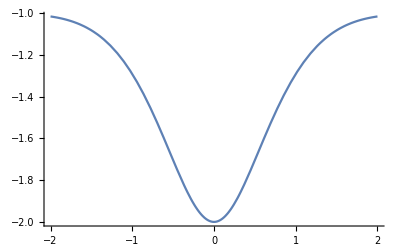

```mathematica
Plot[((x^2/(-1+Exp[-x^2]))-1)*(1/(1+x^2)),{x,-2,2}]
```

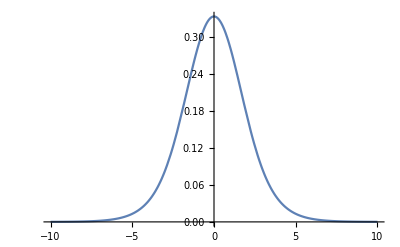

```mathematica
Plot[1/(Cosh[x]+2),{x,-10,10}]
```

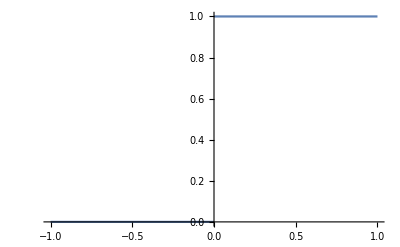

```mathematica
Plot[Piecewise[{{0,x<0},{1,0<x<1}}],{x,-1,1}]
```

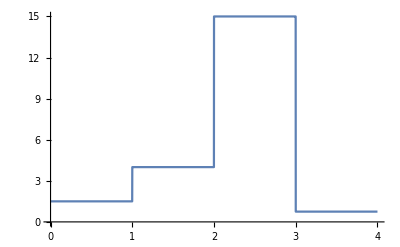

```mathematica
Plot[1.5*WaveletPhi[HaarWavelet[],x]+4*WaveletPhi[HaarWavelet[],x-1]+15*WaveletPhi[HaarWavelet[],x-2]+0.75*WaveletPhi[HaarWavelet[],x-3],{x,0,4},Exclusions->None]
```

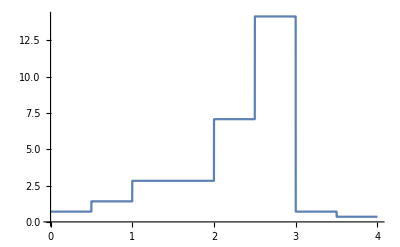

```mathematica
Plot[(0.5*WaveletPhi[HaarWavelet[],2x]+WaveletPhi[HaarWavelet[],2x-1]+2*WaveletPhi[HaarWavelet[],2x-2]+2*WaveletPhi[HaarWavelet[],2x-3]+5*WaveletPhi[HaarWavelet[],2x-4]+10*WaveletPhi[HaarWavelet[],2x-5]+0.5*WaveletPhi[HaarWavelet[],2x-6]+0.25*WaveletPhi[HaarWavelet[],2x-7])*Sqrt[2],{x,0,4},Exclusions->None]
```

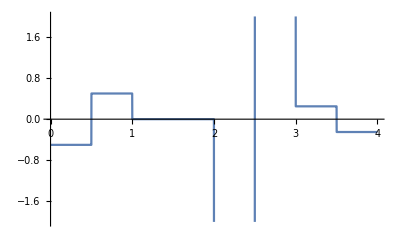

```mathematica
Plot[-0.5*WaveletPsi[HaarWavelet[],x]-5*WaveletPsi[HaarWavelet[],x-2]+0.25*WaveletPsi[HaarWavelet[],x-3],{x,0,4},Exclusions->None]
```

```mathematica
DSolve[{y''[x]+9y[x]== Sin[x]*Cos[x],y[0]==1,y'[0]==0},y[x],x]
```

{{y[x]→1/60 (60 Cos[3 x]-5 Cos[3 x] Sin[x]-4 Sin[3 x]+5 Cos[x] Sin[3 x]-Cos[5 x] Sin[3 x]+Cos[3 x] Sin[5 x])}}

```mathematica
DSolve[{y''[x]-2y'[x]+y[x]== (2x-3)Exp[x],y[0]==1,y'[0]==0},y[x],x]
```

{{y[x]→1/6 ⅇ^x (6-6 x-9 x^2+2 x^3)}}